```mathematica
Subscript[Ψ, 100][r_,θ_,φ_]=SphericalHarmonicY[0,0,θ,φ]*LaguerreL[0,1,2r/(1)]*E^(-r/(1))Sqrt[((0)!/(2*((1)!)))*(2/(1))^3]*(2r/(1))^0
```

ⅇ^-r/(√π)

∫_0^π ∫_0^(2 π) ⅇ^(-2 Re[r_])/π ⅆφⅆθ

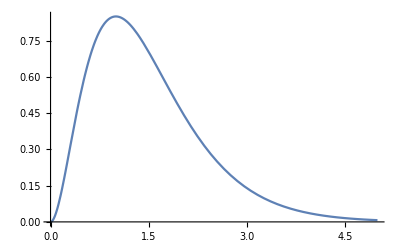

```mathematica
Integrate[Abs[Subscript[Ψ, 100][r_,θ_,φ_]]^2,{θ,0,Pi},{φ,0,2Pi}]
Plot[Integrate[Abs[SphericalHarmonicY[0,0,θ,φ]*LaguerreL[0,1,2r/(1)]*E^(-r/(1))Sqrt[((0)!/(2*((1)!)))*(2/(1))^3]*(2r/(1))^0
]^2,{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,5}]
```

```mathematica
Plot[Integrate[Conjugate[SphericalHarmonicY[0,0,θ,φ]*LaguerreL[0,1,2r/(1)]*E^(-r/(1))Sqrt[((0)!/(2*((1)!)))*(2/(1))^3]*(2r/(1))^0
]*SphericalHarmonicY[0,0,θ,φ]*LaguerreL[0,1,2r/(1)]*E^(-r/(1))Sqrt[((0)!/(2*((1)!)))*(2/(1))^3]*(2r/(1))^0,{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,5}]
```

-Graphics-

```mathematica
NIntegrate[Integrate[Abs[SphericalHarmonicY[0,0,θ,φ]*LaguerreL[0,1,2r/(1)]*E^(-r/(1))Sqrt[((0)!/(2*((1)!)))*(2/(1))^3]*(2r/(1))^0
]^2,{θ,0,Pi},{φ,0,2Pi}]*r^2,{r,0,5}]
```

```mathematica
Integrate[Abs[SphericalHarmonicY[0,0,θ,φ]*LaguerreL[0,1,2r/(1)]*E^(-r/(1))Sqrt[((0)!/(2*((1)!)))*(2/(1))^3]*(2r/(1))^0
]^2,{θ,0,Pi},{φ,0,2Pi}]*r^2
```

```mathematica
Integrate[2 ⅇ^(-2 Re[r]) π r^2,{r,0,Infinity}]
```

π/2

-Graphics-

```mathematica
Subscript[Ψ, nlm][r_,θ_,φ_]=SphericalHarmonicY[l,m,θ,φ]*LaguerreL[n-l-1,2l+1,2r/(n)]*E^(-r/(n))Sqrt[((n-l-1)!/(2n*((n+l)!)))*(2/(n Subscript[a, 0]))^3]*(2r/(n))^l
```